```mathematica
w[r_] := 2/3 - 4 r^2 + 4 r^3/;r≤ 1/2
w[r_] := 4/3 - 4*r + 4*r^2 -4/3*r^3/;1/2 ≤ r ≤ 1
w[r_] := 0/;r>1
```

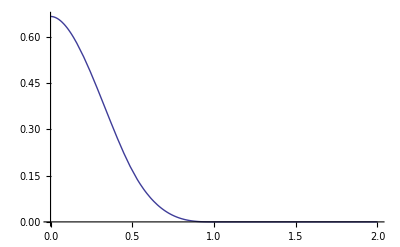

```mathematica
Plot[w[r], {r,0,2}]
```

```mathematica
w[0.5]
```

0.166667

```mathematica
w[0]
```

2/3

```mathematica
w[1]
```

0

```mathematica
Manipulate[Plot[w[Abs[x-0] / di],{x,-1.5 * range,1.5 * range}] ,{di, 1, 10}, {range, 1, 10}]
```

```mathematica
w[r] /. r-> Abs[x - 0]
```

```mathematica
2/3-4 Abs[x]^2+4 Abs[x]^3
di
```

2/3-4 Abs[x]^2+4 Abs[x]^3

```mathematica
dI
```

dI

```mathematica
Manipulate[Plot3D[w[Sqrt[(x-0)^2 + (y-0)^2]/di],{x, -1.5*range, 1.5*range},{y, -1.5*range, 1.5*range}, PlotRange-> All] ,{di,1,10},{range, 1,10}]
```